# Example

## Example for the paper "Bunched Beam Envelope Equations Including Images from a Cylindrical Pipe, C. Allen"

## Auxiliary Functions

## --------------------------------------------------------------------------------------------------- Wr[x] and Wz[s]

```mathematica
q1[s_]=√(1/2-s^2)
```

√(1/2-s^2)

```mathematica
q2[s_]=√(s^2-1/2)
```

√(-1/2+s^2)

```mathematica
Wr[s_]=If[s<1/(√2),ArcTan[q1[s]/s]/(2 q1[s]^3)-s/q1[s]^2,-ArcTanh[q2[s]/s]/(2 q2[s]^3)+s/q2[s]^2]
```

If[s<1/(√2),ArcTan[q1[s]/s]/(2 q1[s]^3)-s/q1[s]^2,-ArcTanh[q2[s]/s]/(2 q2[s]^3)+s/q2[s]^2]

```mathematica
Wz[s_]=If[s<1/(√2),-(s^3 ArcTan[q1[s]/s])/q1[s]^3+s^2/q1[s]^2,(s^3 ArcTanh[q2[s]/s])/q2[s]^3-s^2/q2[s]^2]
```

If[s<1/(√2),-(s^3 ArcTan[q1[s]/s])/q1[s]^3+s^2/q1[s]^2,(s^3 ArcTanh[q2[s]/s])/q2[s]^3-s^2/q2[s]^2]

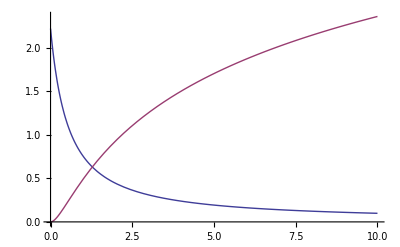

```mathematica
Plot[{Wr[s],Wz[s]},{s,0,10}]
```

## --------------------------------------------------------------------------------------------------- A[x]

```mathematica
Iuni[w_]=((3 Cos[w])/w^2-(3 Sin[w])/w^3+Sin[w]/w) (Cos[w]/w^2-Sin[w]/w^3)
```

(Cos[w]/w^2-Sin[w]/w^3) ((3 Cos[w])/w^2-(3 Sin[w])/w^3+Sin[w]/w)

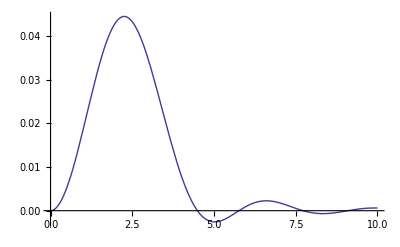

```mathematica
Plot[Iuni[w],{w,0,10}]
```

```mathematica
Bcent[x_,w_]=BesselK[0,w x]/BesselI[0,w x]
```

BesselK[0,w x]/BesselI[0,w x]

```mathematica
Basym[x_,w_]=Exp[-2 w x]
```

ⅇ^(-2 w x)

```mathematica
Asmal[x_]=-1/15 π Log[x/4]-(61 π)/450
```

-(61 π)/450-1/15 π Log[x/4]

```mathematica
Aasym[x_]=2 ∫_0^∞ Iuni[w] Basym[x,w]ⅆw
```

2 ∫_0^∞ ⅇ^(-2 w x) (Cos[w]/w^2-Sin[w]/w^3) ((3 Cos[w])/w^2-(3 Sin[w])/w^3+Sin[w]/w)ⅆw

```mathematica
∫_0^∞ (Cos[w]^2 Exp[-2 x w])/w^4 ⅆw
```

Integrate::idiv: Integral of ⅇ^-2 w x Cos[w]^2/w^4 does not converge on {0, ∞}.

∫_0^∞ (ⅇ^(-2 w x) Cos[w]^2)/w^4 ⅆw

```mathematica
Acent[x_]:=2 NIntegrate[Iuni[w] Bcent[x,w],{w,0,∞}]
```

```mathematica
AcentTable=Table[{x,Acent[x]},{x,0.3,5.0,0.1}]
```

{{0.3,0.143986},{0.4,0.100598},{0.5,0.0722942},{0.6,0.0531552},{0.7,0.0398764},{0.8,0.0304642},{0.9,0.0236641},{1.,0.0186638},{1.1,0.0149264},{1.2,0.0120903},{1.3,0.00990742},{1.4,0.00820527},{1.5,0.0068618},{1.6,0.00578949},{1.7,0.00492468},{1.8,0.0042205},{1.9,0.00364199},{2.,0.00316279},{2.1,0.0027628},{2.2,0.00242654},{2.3,0.00214198},{2.4,0.00189968},{2.5,0.00169216},{2.6,0.00151347},{2.7,0.00135882},{2.8,0.00122434},{2.9,0.00110688},{3.,0.00100384},{3.1,0.000913109},{3.2,0.000832905},{3.3,0.000761758},{3.4,0.000698434},{3.5,0.000641893},{3.6,0.000591256},{3.7,0.000545777},{3.8,0.00050482},{3.9,0.000467838},{4.,0.000434364},{4.1,0.000403993},{4.2,0.000376376},{4.3,0.000351209},{4.4,0.000328226},{4.5,0.000307198},{4.6,0.000287922},{4.7,0.000270219},{4.8,0.000253932},{4.9,0.000238925},{5.,0.000225073}}

```mathematica
AcentInterp=Interpolation[AcentTable]
```

InterpolatingFunction[{{0.3,5.}},<>]

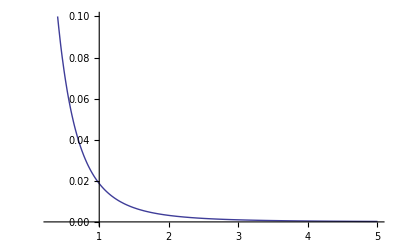

```mathematica
Plot[{AcentInterp[x]},{x,0.3,5.0},PlotRange->{0,0.1}]
```

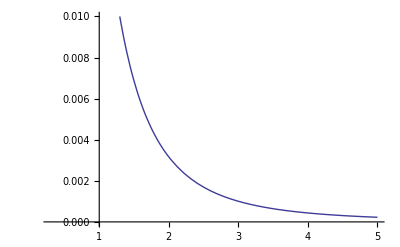

```mathematica
Plot[{AcentInterp[x]},{x,0.3,5.0},PlotRange->{0,0.01}]
```

```mathematica
A[x_]=Which[x<0.3,Asmal[x],x<5.0,AcentInterp[x],True,0]
```

Which[x<0.3,Asmal[x],x<5.,AcentInterp[x],True,0]

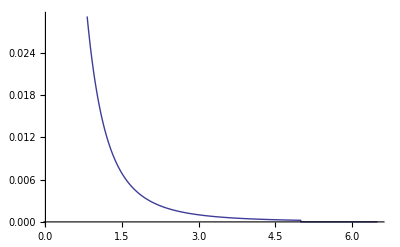

```mathematica
Plot[{A[x]},{x,0.1,6.5}]
```

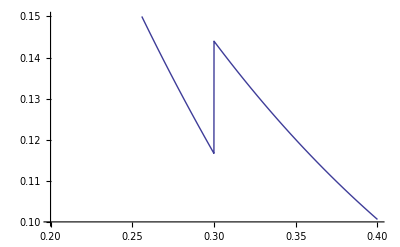

```mathematica
Plot[{A[x]},{x,0.2,0.4},PlotRange->{0.1,0.15}]
```

```mathematica
AcentInterp[0.3]-Asmal[0.3]
```

0.0273423

```mathematica
Asmal[x_]=Asmal[x]+AcentInterp[0.3]-Asmal[0.3]
```

-0.398518-1/15 π Log[x/4]

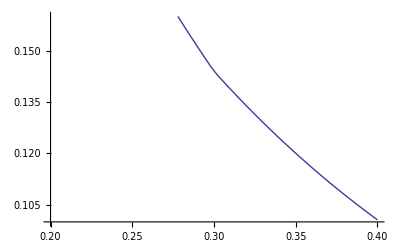

```mathematica
Plot[{A[x]},{x,0.2,0.4},PlotRange->{0.1,0.16}]
```

## --------------------------------------------------------------------------------------------------- The Differential Equation

### Constants

```mathematica
K=0.005;
er=1/10^5;
ez=1/10^5;
```

```mathematica
lz=0.05;
Sz0=0.250;
```

R0  = 0.01;
Rp0 = 0.0;
Z0  = 0.05;
Zp0 = 0.0;

```mathematica
R0=0.01;
Rp0=0.0;
Z0=0.05;
Zp0=0.0;
```

kr0 = K/R0^2;
kz0 = (3/2)(K/Z0^3)(Sz0/lz);

```mathematica
kr0=100;
kz0=200;
```

```mathematica
kr0
```

100

```mathematica
kz0
```

200

### Focusing Function

```mathematica
kr[z_]:=kr0
```

```mathematica
Clear[kzComp]
```

```mathematica
kzComp[z_]:=Which[z<-lz/2,0,z<lz/2,kz0,True,0]
```

```mathematica
kz[z_]:=∑_(n=0)^3 kzComp[z-(n+0.5) Sz0]
```

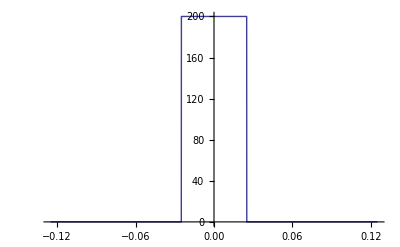

```mathematica
Plot[kzComp[z],{z,-Sz0/2,Sz0/2}]
```

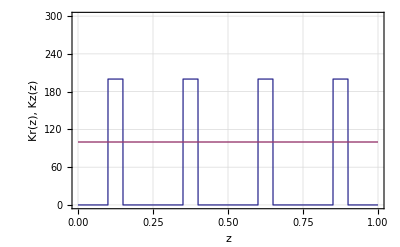

```mathematica
Plot[{kz[z],kr[z]},{z,0,4 Sz0},PlotRange->{0,300},Frame->True,GridLines->Automatic,FrameLabel->{"z","Kr(z), Kz(z)"}]
```

### Compute the matched beam solution

```mathematica
Clear[R];
Clear[Rp];
Clear[Zx];
Clear[Zxp];
Clear[fsSol];
```

```mathematica
error=1;
maxError=1/10^8;
```

```mathematica
While[error>maxError,fsSol=NDSolve[{R'[z]==Rp[z],
                                                                               Rp'[z]==-kr[z] R[z]+(3 K Wr[Zx[z]/(√2 R[z])])/((4 √5) R[z]^2)+er^2/R[z]^3,
                                                                               Zx'[z]==Zxp[z],
                                                                             Zxp'[z]==-kz[z] Zx[z]+(3 K Wz[Zx[z]/(√2 R[z])])/(2 Zx[z]^2)+ez^2/Zx[z]^3,
                                                                                  R[0]==R0,Rp[0]==Rp0,
                                                                                Zx[0]==Z0,Zxp[0]==Zp0},
                                                                                  {R,Rp,Zx,Zxp},{z,0,1 Sz0}];Rave=1/2 (R0+R[Sz0]/.fsSol⟦1⟧);Rpave=1/2 (Rp0+Rp[Sz0]/.fsSol⟦1⟧);Zave=1/2 (Z0+Zx[Sz0]/.fsSol⟦1⟧);Zpave=1/2 (Zp0+Zxp[Sz0]/.fsSol⟦1⟧);error=(R0-Rave)^2+(Rp0-Rpave)^2+(Z0-Zave)^2+(Zp0-Zpave)^2;R0=Rave;Rp0=Rpave;Z0=Zave;Zp0=Zpave;]
```

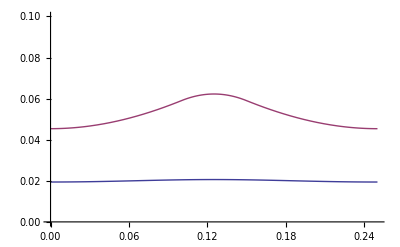

```mathematica
Plot[{R[z]/.fsSol,Zx[z]/.fsSol},{z,0,1 Sz0},PlotRange->{0,0.1}]
```

### These are the envelope parameters for the matched beam

```mathematica
R0
```

0.0194115

```mathematica
Rp0
```

0.0000222306

```mathematica
Z0
```

0.0453701

```mathematica
Zp0
```

0.0000125663

### Now look what happens over 4 periods

```mathematica
fsSol=NDSolve[{R'[z]==Rp[z],Rp'[z]==-kr[z] R[z]+(3 K Wr[Zx[z]/(√2 R[z])])/((4 √5) R[z]^2)+er^2/R[z]^3,Zx'[z]==Zxp[z],Zxp'[z]==-kz[z] Zx[z]+(3 K Wz[Zx[z]/(√2 R[z])])/(2 Zx[z]^2)+ez^2/Zx[z]^3,R[0]==R0,Rp[0]==Rp0,Zx[0]==Z0,Zxp[0]==Zp0},{R,Rp,Zx,Zxp},{z,0,4 Sz0},MaxSteps->1000]
```

{{R→InterpolatingFunction[{{0.,1.}},<>],Rp→InterpolatingFunction[{{0.,1.}},<>],Zx→InterpolatingFunction[{{0.,1.}},<>],Zxp→InterpolatingFunction[{{0.,1.}},<>]}}

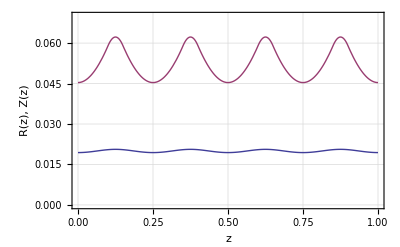

```mathematica
Plot[{R[z]/.fsSol,Zx[z]/.fsSol},{z,0,4 Sz0},PlotRange->{0,0.07},Frame->True,GridLines->Automatic,FrameLabel->{"z","R(z), Z(z)"}]
```

### Now compute matched beam with Images from pipe with radius b

```mathematica
b=0.05;
```

```mathematica
Clear[R];
Clear[Rp];
Clear[Zx];
Clear[Zxp];
Clear[iSol]
```

```mathematica
error=1;
maxError=1/10^7;
```

```mathematica
While[error>maxError,iSol=NDSolve[{R'[z]==Rp[z],Rp'[z]==-kr[z] R[z]+(3 K Wr[Zx[z]/(√2 R[z])])/((4 √5) R[z]^2)+(45 K R[z] A[b/(√(Zx[z]^2-R[z]^2))])/(2 (Zx[z]^2-R[z]^2)^(3/2))+er^2/R[z]^3,Zx'[z]==Zxp[z],Zxp'[z]==-kz[z] Zx[z]+(3 K Wz[Zx[z]/(√2 R[z])])/(2 Zx[z]^2)-(45 K Zx[z] A[b/(√(Zx[z]^2-R[z]^2))])/(2 (Zx[z]^2-R[z]^2)^(3/2))+ez^2/Zx[z]^3,R[0]==R0,Rp[0]==Rp0,Zx[0]==Z0,Zxp[0]==Zp0},{R,Rp,Zx,Zxp},{z,0,1 Sz0}];Rave=1/2 (R0+R[Sz0]/.iSol⟦1⟧);Rpave=1/2 (Rp0+Rp[Sz0]/.iSol⟦1⟧);Zave=1/2 (Z0+Zx[Sz0]/.iSol⟦1⟧);Zpave=1/2 (Zp0+Zxp[Sz0]/.iSol⟦1⟧);error=(R0-Rave)^2+(Rp0-Rpave)^2+(Z0-Zave)^2+(Zp0-Zpave)^2;R0=Rave;Rp0=Rpave;Z0=Zave;Zp0=Zpave;]
```

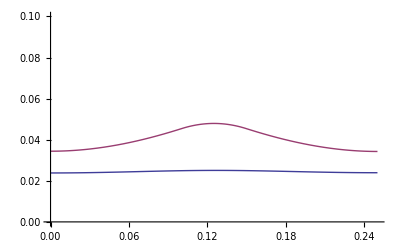

```mathematica
Plot[{R[z]/.iSol,Zx[z]/.iSol},{z,0,1 Sz0},PlotRange->{0,0.1}]
```

### These are the envelope parameters for the matched beam

```mathematica
R0
```

0.023878

```mathematica
Rp0
```

0.0000570581

```mathematica
Z0
```

0.0343454

```mathematica
Zp0
```

-0.000667525

### Now look at what happens over 4 periods

```mathematica
iSol=NDSolve[{R'[z]==Rp[z],Rp'[z]==-kr[z] R[z]+(3 K Wr[Zx[z]/(√2 R[z])])/((4 √5) R[z]^2)+(45 K R[z] A[b/(√(Zx[z]^2-R[z]^2))])/(2 (Zx[z]^2-R[z]^2)^(3/2))+er^2/R[z]^3,Zx'[z]==Zxp[z],Zxp'[z]==-kz[z] Zx[z]+(3 K Wz[Zx[z]/(√2 R[z])])/(2 Zx[z]^2)-(45 K Zx[z] A[b/(√(Zx[z]^2-R[z]^2))])/(2 (Zx[z]^2-R[z]^2)^(3/2))+ez^2/Zx[z]^3,R[0]==R0,Rp[0]==Rp0,Zx[0]==Z0,Zxp[0]==Zp0},{R,Rp,Zx,Zxp},{z,0,4 Sz0},MaxSteps->1000]
```

{{R→InterpolatingFunction[{{0.,1.}},<>],Rp→InterpolatingFunction[{{0.,1.}},<>],Zx→InterpolatingFunction[{{0.,1.}},<>],Zxp→InterpolatingFunction[{{0.,1.}},<>]}}

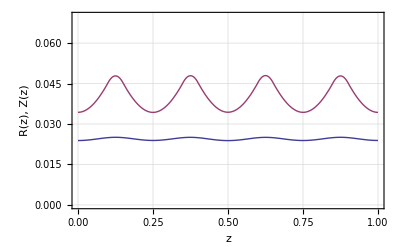

```mathematica
Plot[{R[z]/.iSol,Zx[z]/.iSol},{z,0,4 Sz0},PlotRange->{0,0.07},Frame->True,GridLines->Automatic,FrameLabel->{"z","R(z), Z(z)"}]
```

## --------------------------------------------------------------------------------------------------- NOT USED

```mathematica
Plot[A[x],{x,0,6.5},GridLines->Automatic,PlotRange->{0,0.1}]
```

Plot::plnr: 
   CompiledFunction[{x}, <<1>>, <<12>>e-][x]
     is not a machine-size real number at x = 0..

⁃Graphics⁃